# Across Model Evaluations

## Occurrences of layers

```mathematica
frameworkName="TensorFlow";
frameworkVersion="1.12";
dirs=Union[DirectoryName/@FileNames["model_info.json","~/experiments/"<>frameworkName<>"/"<>frameworkVersion<>"/",Infinity]];
```

```mathematica
opNames=Association@Table[
json=Import[FileNameJoin[{dir,"model_info.json"}],"RawJSON"];
modelName=FileNameTake[dir,{5}];
modelName->Lookup[json["node"],"op"],
{dir,dirs}
];
```

```mathematica
dist=Select[
Sort[Counts[
Select[
Flatten[Values[opNames]],
FreeQ[{"Const","Placeholder","Identity","TFLite_Detection_PostProcess"},#]&
]
]],#>1000&];
```

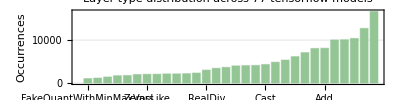

```mathematica
BarChart[dist,
ChartStyle->RGBColor["#94C595"],
PlotLabel->"Layer type distribution across "<>ToString[Length[dirs]]<>" tensorflow models",
FrameLabel->{"Layer Type","Occurrences"},
ChartLabels->(Rotate[#,90Degree]&/@Keys[dist]),AspectRatio->1/4,ImageSize->Scaled[0.75],PlotTheme->"Detailed"
]
```

## Latency of layers

```mathematica
frameworkName="TensorFlow";
frameworkVersion="1.12";
machineName="ip-172-31-20-197";
dirs=Union[DirectoryName/@Select[FileNames["trace_model_trace.json","~/experiments/"<>frameworkName<>"/"<>frameworkVersion<>"/",Infinity],Function[{path},
StringContainsQ[path,"/1/gpu/"]&&StringContainsQ[path,machineName]
]
]];
```

```mathematica
layerInfoOf[Nothing]:=Missing[Nothing];
layerInfoOf[op_String]:=Module[{info=SelectFirst[modelInfo,#["op"]===op&]},
If[MissingQ[info],Return[info]];
ImportString[info["attr"]["op_info"]["Value"]["Placeholder"],"RawJSON"]
];
layerInfoOf[span_?AssociationQ]:=layerInfoOf[opNameOf[span]];
```

```mathematica
operationNamedQ[name_][e_]:=e["operationName"]===name;
ClearAll[nameOf];
hasTag[span_,name_]:=With[{tags=span["tags"]},!MissingQ[SelectFirst[tags,#["key"]===name&]]];
hasTagValue[span_,name_,value_]:=With[{tags=span["tags"]},!MissingQ[SelectFirst[tags,#["key"]===name&&#["value"]===value&]]];
getTag[span_,name_]:=With[{tags=span["tags"]},With[{tag=SelectFirst[tags,#["key"]===name&]},If[MissingQ[tag],Nothing,tag["value"]]]];
nameOf[span_?(operationNamedQ["gpu_kernel"])]:=With[{tags=span["tags"]},SelectFirst[tags,#["key"]==="name"&]["value"]];
nameOf[span_]:=With[{tags=span["tags"]},
With[{n=SelectFirst[tags,#["key"]==="function_name"&]},
If[MissingQ[n],span["operationName"],n["value"]]]];
summaryNameOf[span_]:=With[{e=nameOf[span]},
If[KeyExistsQ[layerSummary,e],layerSummary[e],e]];
layerIndexOf[span_]:=With[{tags=span["tags"]},
With[{n=SelectFirst[tags,#["key"]==="layer_sequence_index"&]},
If[MissingQ[n],n,n["value"]]]]
```

```mathematica
ClearAll[layerNameOf];
layerNameOf1[span_]:=With[{s=getTag[span,"timeline_label"]},With[{case=StringCases[s,___~~" = "~~Shortest[name__]~~"("~~___->name]},If[case=={},Nothing,First[case]]]];
layerNameOf[span_]:=With[{s=span["operationName"]},SelectFirst[modelInfo,#["name"]===s&]];
opNameOf[span_]:=With[{opInfo=layerNameOf[span]},If[MissingQ[opInfo]||opInfo==={},Nothing,opInfo["op"]]];
summaryOpNameOf[span_]:=With[{e=opNameOf[span]},
If[KeyExistsQ[layerSummary,e],layerSummary[e],e]];
```

```mathematica
durations=Association@Table[
json=Import[FileNameJoin[{dir,"trace_framework_trace.json"}],"RawJSON"];
modelInfo=Import[FileNameJoin[{dir,"..","..","..","model_info.json"}],"RawJSON"]["node"];
allSpans=Select[
First[json["data"]]["spans"],!MemberQ[{"RecvTensor","_SOURCE"},#["operationName"]]&
];

start=SelectFirst[allSpans,#["operationName"]==="c_predict"&]["startTime"];
end=SelectFirst[allSpans,#["operationName"]==="read_predicted_features"&]["startTime"];
spans=Select[allSpans,#["startTime"]>start&&#["startTime"]<end&&#["operationName"]=!="launch_kernel"&];

spans=Select[spans,MemberQ[Lookup[#["tags"],"key"],"layer_sequence_index"]&&opNameOf[#]=!="WaitForVar"&];
modelName=FileNameTake[dir,{5}];
modelName->(If[MissingQ[layerInfoOf[#]],Nothing,layerInfoOf[#]["name"]->#["duration"]]&/@Select[spans,MemberQ[Lookup[#["tags"],"key"],"layer_sequence_index"]&]),
{dir,dirs[[;;9]]}
];
```

```mathematica
ClearAll[colorOf];
ClearAll[icolorOf];
colorOf[Nothing]=Gray;
colorOf[s_]:=icolorOf[ToLowerCase[s]];
icolorOf["const"]=RGBColor["#284005"];
icolorOf["biasadd"]=Orange;
icolorOf["convolution"|"conv2d"]=RGBColor["#284595"];
icolorOf["activation"|"relu"]=RGBColor["#465362"];
icolorOf["pooling"|"maxpool"|"avgpool"]=RGBColor["#D51745"];
icolorOf["lrn"]=RGBColor["#94C595"];
icolorOf["dropout"]=RGBColor["#14C595"];
icolorOf["add"|"mul"|"mean"]=Darker[Yellow];
icolorOf["flatten"|"concatv2"|"pad"|"padv2"|"stridedslice"]=RGBColor["#000"];
icolorOf["softmaxoutput"|"softmax"]=RGBColor["#697A55"];
icolorOf["fullyconnected"|"matmul"]=RGBColor["#FD6A02"];
icolorOf["pad"|"padv2"]=RGBColor["#763262"];
icolorOf["concatv2"]=RGBColor["#CA7508"];
icolorOf[v__]:=ColorData[3,"ColorList"][[Mod[Hash[v,"CRC32"],10]+1]];
```

```mathematica
keys=Union[Flatten[{Keys[Values[durations]]}]];
SwatchLegend[colorOf/@keys,keys]
```

```mathematica
GraphicsGrid[
Partition[
Table[
duration=Merge[durations[name],Total];
duration=SortBy[Normal[duration]/.Rule->(Tooltip[Style[#2,colorOf[#1]],#1]&),First];
If[StringLength[name]>25,
name=StringTake[name,25]<>"\n"<>StringDrop[name,25]
];
PieChart[duration,
PlotTheme->{"Grid","VibrantColor"},
ImageMargins->30,
ImageSize->Scaled[0.3],
PlotRangeClipping->False,
PlotLabel-> Style[name,FontSize->10]
],
{name,Keys[durations]}
],4
],
ImageSize->Scaled[0.9]
]
```

-Graphics-

### for tree map

```mathematica
dirs[[9]]
```

~/experiments/TensorFlow/1.12/Faster_RCNN_Inception_ResNet_v2_Atrous_Lowproposals_COCO/1.0/1/gpu/ip-172-31-20-197/

```mathematica
dir=dirs[[9]];
json=Import[FileNameJoin[{dir,"trace_framework_trace.json"}],"RawJSON"];
modelInfo=Import[FileNameJoin[{dir,"..","..","..","model_info.json"}],"RawJSON"]["node"];
allSpans=Select[
First[json["data"]]["spans"],!MemberQ[{"RecvTensor","_SOURCE"},#["operationName"]]&
];
```

```mathematica
start=SelectFirst[allSpans,#["operationName"]==="c_predict"&]["startTime"];
end=SelectFirst[allSpans,#["operationName"]==="read_predicted_features"&]["startTime"];
spans=Select[allSpans,#["startTime"]>start&&#["startTime"]<end&&#["operationName"]=!="launch_kernel"&];

spans=Select[spans,MemberQ[Lookup[#["tags"],"key"],"layer_sequence_index"]&&opNameOf[#]=!="WaitForVar"&];
modelName=FileNameTake[dir,{5}];
```

```mathematica
duration=If[MissingQ[layerInfoOf[#]],Nothing,layerInfoOf[#]["name"]-><|
"opName"->#["operationName"],
"duration"->#["duration"]|>]&/@Select[spans,MemberQ[Lookup[#["tags"],"key"],"layer_sequence_index"]&];
```

```mathematica
Select[duration,First[#]==="Relu6"&];
```

```mathematica
tree=Map[
Function[{key},
<|
"name"->key,
"value"->Total[Lookup[Select[duration,First[#]===key&][[All,2]] ,"duration"]],
"children"->Table[
If[First[t]===key, 
<|
"name"->key,
"value"->t[[2]]["duration"],
"node_name"->t[[2]]["opName"]
|>,
Nothing
],
{t,duration}
]
|>
],
Union[First/@duration]
];
```

```mathematica
Export["~/Downloads/treemap/data.json",tree,"JSON"]
```

~/Downloads/treemap/data.json

```mathematica
ExportString[tree,"JSON","Compact"->True]//CopyToClipboard
```

```mathematica
GroupBy[durations[[1]],First]
```

<|Conv2D→{Conv2D→80,Conv2D→49,Conv2D→48,Conv2D→62,Conv2D→46,Conv2D→49,Conv2D→48,Conv2D→47},LRN→{LRN→21,LRN→20},Pad→{Pad→42,Pad→18,Pad→19,Pad→17,Pad→17},Relu→{Relu→12,Relu→11,Relu→11},Add→{Add→20,Add→15,Add→14,Add→13,Add→15},PadV2→{PadV2→18,PadV2→18,PadV2→17},MaxPool→{MaxPool→22,MaxPool→26,MaxPool→22},ConcatV2→{ConcatV2→25,ConcatV2→32,ConcatV2→25},Split→{Split→15,Split→16,Split→17},StridedSlice→{StridedSlice→11},MatMul→{MatMul→48,MatMul→25,MatMul→26},BiasAdd→{BiasAdd→14,BiasAdd→12,BiasAdd→12},Softmax→{Softmax→31}|>

## All Image Classification Models

```mathematica
frameworkName="TensorFlow";
frameworkVersion="1.12";
machineName="ip-172-31-20-197";
dirs=Union[DirectoryName/@Select[FileNames["trace_model_trace.json","~/experiments/"<>frameworkName<>"/"<>frameworkVersion<>"/",Infinity],Function[{path},
StringContainsQ[path,"/1/gpu/"]&&StringContainsQ[path,machineName]
]
]];
dirs=Select[
dirs,
Function[{dir},
json=Import[FileNameJoin[{dir,"..","..","..","manifest.json"}],"RawJSON"];
json["output"]["type"]==="classification"&&
!MissingQ[json["attributes"]["top1"]]
]
];
```

```mathematica
baseModelDir=FileNameTake[#,6]&/@dirs;
allNetInfo=Association@Table[
es=Import[file,"RawJSON"];
ToLowerCase[FileNameTake[file,{5}]]-><|"Top1"->ToExpression[es["attributes"]["top1"]],"Top5"->ToExpression[es["attributes"]["top5"]]|>,
{file,FileNames["manifest.json",baseModelDir]}
];
```

```mathematica
durations=Association@Table[
json=Import[FileNameJoin[{dir,"trace_model_trace.json"}],"RawJSON"];
allSpans=First[json["data"]]["spans"];
modelName=FileNameTake[dir,{5}];
modelName->Lookup[SelectFirst[allSpans,#["operationName"]==="c_predict"&],"duration"]/1000.,
{dir,dirs}
];
```

```mathematica
modelSizes=Association@Table[
json=Import[FileNameJoin[{dir,"..","..","..","model_info.json"}],"RawJSON"];
numParams=Total[
Apply[Times,#]&/@Lookup[json["tensor_infos"],"dims",{}]
]/ (1000.*1000);
modelName=FileNameTake[dir,{5}];
modelName->numParams,
{dir,dirs}
];
```

```mathematica
infoKeyName[key0_]:=With[{key=ToLowerCase[key0]},
Which[
KeyExistsQ[allNetInfo,key],key,
KeyExistsQ[allNetInfo,StringReplace[key,"0.50"->"0.5"]],StringReplace[key,"0.50"->"0.5"],
KeyExistsQ[allNetInfo,StringReplace[key,"0.5"->"0.50"]],StringReplace[key,"0.5"->"0.50"],
True,Missing["KeyAbsent",key]
]];
top1[key0_]:=With[{key=infoKeyName[key0]},
If[MissingQ[key],key,allNetInfo[key]["Top1"]]];
mac[key0_]:=With[{key=infoKeyName[key0]},
If[MissingQ[key],key,allNetInfo[key]["MACs"]]];
```

```mathematica
BubbleChart[
Table[Callout[{durations[key],top1[key],modelSizes[key]},key],{key,Keys[durations]}],
PlotTheme->"Detailed",
ChartStyle->RGBColor["#94C595"],
AspectRatio->1/(1.5*GoldenRatio),
ImageSize->Scaled[0.7],
PlotRange->All,
PlotLabel->ToString[Length[durations]]<>" Classification Models Latency/Accuracy Tradeoff",
FrameLabel->{"Latency(ms)","Top1 Accuracy"}
]
```

-Graphics-

```mathematica
BubbleChart[
Table[Callout[{durations[key],top1[key],modelSizes[key]},key,Appearance->"Leader"],{key,Select[Keys[durations],!StringContainsQ[#,"VGG"]&&!StringContainsQ[#,"Inception_5h"]&]}],
PlotTheme->"Detailed",
ChartStyle->RGBColor["#94C595"],
AspectRatio->1/(1.5*GoldenRatio),
ImageSize->Scaled[0.7],
PlotRange->All,
PlotLabel->ToString[Length[durations]]<>" Classification Models Latency/Accuracy Tradeoff Ignoring Outliers",
FrameLabel->{"Latency(ms)","Top1 Accuracy"}
]
```

-Graphics-

```mathematica
BubbleChart[
Table[Callout[{durations[key],top1[key],modelSizes[key]},key],{key,Keys[durations]}],
PlotTheme->"Detailed",
ChartStyle->RGBColor["#94C595"],
AspectRatio->1/(1.5*GoldenRatio),
ImageSize->Scaled[0.7],
PlotRange->All,
PlotLabel->ToString[Length[durations]]<>" Classification Models Latency/Accuracy Tradeoff",
FrameLabel->{"Latency(ms)","Top1 Accuracy"}
]
```

-Graphics-

## Mobile Net CPU

### Static Data

Copy the table as a string from https://github.com/tensorflow/models/blob/master/research/slim/nets/mobilenet_v1.md#pre-trained-models and use the following script to process

d = Rest[ImportString[s, "TSV"]];
mobileNetInfo = AssociationThread[ToLowerCase[d[[All, 1]]] ->
   Map[AssociationThread[{"MACs", "Parameters", "Top1", "Top5"} -> #] &, d[[All, 2 ;;]]]]

```mathematica
mobileNetInfo=<|"mobilenet_v1_1.0_224"-><|"MACs"->569,"Parameters"->4.24,"Top1"->70.9,"Top5"->89.9|>,"mobilenet_v1_1.0_192"-><|"MACs"->418,"Parameters"->4.24,"Top1"->70.,"Top5"->89.2|>,"mobilenet_v1_1.0_160"-><|"MACs"->291,"Parameters"->4.24,"Top1"->68.,"Top5"->87.7|>,"mobilenet_v1_1.0_128"-><|"MACs"->186,"Parameters"->4.24,"Top1"->65.2,"Top5"->85.8|>,"mobilenet_v1_0.75_224"-><|"MACs"->317,"Parameters"->2.59,"Top1"->68.4,"Top5"->88.2|>,"mobilenet_v1_0.75_192"-><|"MACs"->233,"Parameters"->2.59,"Top1"->67.2,"Top5"->87.3|>,"mobilenet_v1_0.75_160"-><|"MACs"->162,"Parameters"->2.59,"Top1"->65.3,"Top5"->86.|>,"mobilenet_v1_0.75_128"-><|"MACs"->104,"Parameters"->2.59,"Top1"->62.1,"Top5"->83.9|>,"mobilenet_v1_0.50_224"-><|"MACs"->150,"Parameters"->1.34,"Top1"->63.3,"Top5"->84.9|>,"mobilenet_v1_0.50_192"-><|"MACs"->110,"Parameters"->1.34,"Top1"->61.7,"Top5"->83.6|>,"mobilenet_v1_0.50_160"-><|"MACs"->77,"Parameters"->1.34,"Top1"->59.1,"Top5"->81.9|>,"mobilenet_v1_0.50_128"-><|"MACs"->49,"Parameters"->1.34,"Top1"->56.3,"Top5"->79.4|>,"mobilenet_v1_0.25_224"-><|"MACs"->41,"Parameters"->0.47,"Top1"->49.8,"Top5"->74.2|>,"mobilenet_v1_0.25_192"-><|"MACs"->34,"Parameters"->0.47,"Top1"->47.7,"Top5"->72.3|>,"mobilenet_v1_0.25_160"-><|"MACs"->21,"Parameters"->0.47,"Top1"->45.5,"Top5"->70.3|>,"mobilenet_v1_0.25_128"-><|"MACs"->14,"Parameters"->0.47,"Top1"->41.5,"Top5"->66.3|>,"mobilenet_v1_1.0_224_quant"-><|"MACs"->569,"Parameters"->4.24,"Top1"->70.1,"Top5"->88.9|>,"mobilenet_v1_1.0_192_quant"-><|"MACs"->418,"Parameters"->4.24,"Top1"->69.2,"Top5"->88.3|>,"mobilenet_v1_1.0_160_quant"-><|"MACs"->291,"Parameters"->4.24,"Top1"->67.2,"Top5"->86.7|>,"mobilenet_v1_1.0_128_quant"-><|"MACs"->186,"Parameters"->4.24,"Top1"->63.4,"Top5"->84.2|>,"mobilenet_v1_0.75_224_quant"-><|"MACs"->317,"Parameters"->2.59,"Top1"->66.8,"Top5"->87.|>,"mobilenet_v1_0.75_192_quant"-><|"MACs"->233,"Parameters"->2.59,"Top1"->66.1,"Top5"->86.4|>,"mobilenet_v1_0.75_160_quant"-><|"MACs"->162,"Parameters"->2.59,"Top1"->62.3,"Top5"->83.8|>,"mobilenet_v1_0.75_128_quant"-><|"MACs"->104,"Parameters"->2.59,"Top1"->55.8,"Top5"->78.8|>,"mobilenet_v1_0.50_224_quant"-><|"MACs"->150,"Parameters"->1.34,"Top1"->60.7,"Top5"->83.2|>,"mobilenet_v1_0.50_192_quant"-><|"MACs"->110,"Parameters"->1.34,"Top1"->60.,"Top5"->82.2|>,"mobilenet_v1_0.50_160_quant"-><|"MACs"->77,"Parameters"->1.34,"Top1"->57.7,"Top5"->80.4|>,"mobilenet_v1_0.50_128_quant"-><|"MACs"->49,"Parameters"->1.34,"Top1"->54.5,"Top5"->77.7|>,"mobilenet_v1_0.25_224_quant"-><|"MACs"->41,"Parameters"->0.47,"Top1"->48.,"Top5"->72.8|>,"mobilenet_v1_0.25_192_quant"-><|"MACs"->34,"Parameters"->0.47,"Top1"->46.,"Top5"->71.2|>,"mobilenet_v1_0.25_160_quant"-><|"MACs"->21,"Parameters"->0.47,"Top1"->43.4,"Top5"->68.5|>,"mobilenet_v1_0.25_128_quant"-><|"MACs"->14,"Parameters"->0.47,"Top1"->39.5,"Top5"->64.4|>|>;
```

### plot

```mathematica
frameworkName="TensorFlow";
frameworkVersion="1.12";
modelBaseName="MobileNet";
machineName="ip-172-31-20-197";
modelVersion="1.0";
dirs=Union[DirectoryName/@Select[FileNames["trace_model_trace.json","~/experiments/"<>frameworkName<>"/"<>frameworkVersion<>"/",Infinity],Function[{path},
StringContainsQ[path,"/1/cpu/"]&&StringContainsQ[path,machineName]&&StringContainsQ[path,"/"<>modelBaseName]
]
]];
```

```mathematica
durations=Association@Table[
json=Import[FileNameJoin[{dir,"trace_model_trace.json"}],"RawJSON"];
allSpans=First[json["data"]]["spans"];
modelName=FileNameTake[dir,{5}];
modelName->Lookup[SelectFirst[allSpans,#["operationName"]==="c_predict"&],"duration"]/1000,
{dir,dirs}
];
```

```mathematica
modelSizes=Association@Table[
json=Import[FileNameJoin[{dir,"..","..","..","model_info.json"}],"RawJSON"];
numParams=Total[
Apply[Times,#]&/@Lookup[json["tensor_infos"],"dims",{}]
]/ (1000.*1000);
modelName=FileNameTake[dir,{5}];
modelName->numParams,
{dir,dirs}
];
```

```mathematica
infoKeyName[key0_]:=With[{key=ToLowerCase[key0]},
Which[
KeyExistsQ[mobileNetInfo,key],key,
KeyExistsQ[mobileNetInfo,StringReplace[key,"0.50"->"0.5"]],StringReplace[key,"0.50"->"0.5"],
KeyExistsQ[mobileNetInfo,StringReplace[key,"0.5"->"0.50"]],StringReplace[key,"0.5"->"0.50"],
True,Missing["KeyAbsent",key]
]];
top1[key0_]:=With[{key=infoKeyName[key0]},
If[MissingQ[key],key,mobileNetInfo[key]["Top1"]]];
mac[key0_]:=With[{key=infoKeyName[key0]},
If[MissingQ[key],key,mobileNetInfo[key]["MACs"]]];
```

```mathematica
p=Graphics[{Opacity[0.5],EdgeForm[{Black,Thick}],FaceForm[RGBColor["#94C595"]],Disk[]}];
ListPlot[
Table[Callout[Style[{durations[key],top1[key]},EdgeForm[{Black,Thickness[0.02]}],PointSize[modelSizes[key]/50]],key],{key,Keys[durations]}],
PlotTheme->"Detailed",
ImageSize->Scaled[0.7],
PlotRange->All,
PlotMarkers->{p,.1},
PlotLabel->"MobileNet Latency/Accuracy Tradeoff"
];
BubbleChart[
Table[Callout[{durations[key],top1[key],modelSizes[key]},StringTrim[key,"MobileNet_v1_"]],{key,Keys[durations]}],
PlotTheme->"Detailed",
ImageSize->Scaled[0.6],
ChartStyle->RGBColor["#94C595"],
AspectRatio->1/(1.5*GoldenRatio),
PlotRange->All,
PlotLabel->"MobileNet Latency/Accuracy Tradeoff on CPU",
FrameLabel->{"Latency(ms)","Top1 Accuracy"}
]
```

-Graphics-

```mathematica
p=Graphics[{Opacity[0.5],EdgeForm[{Black,Thick}],FaceForm[RGBColor["#94C595"]],Disk[]}];
ListPlot[
Table[Callout[Style[{mac[key],top1[key]},EdgeForm[{Black,Thickness[0.02]}],PointSize[modelSizes[key]/50]],key],{key,Keys[durations]}],
PlotTheme->"Detailed",
ImageSize->Scaled[0.7],
PlotRange->All,
PlotMarkers->{p,.1},
PlotLabel->"MobileNet MillionMAC/Accuracy Tradeoff"
];
BubbleChart[
Table[Callout[{mac[key],top1[key],modelSizes[key]},StringTrim[key,"MobileNet_v1_"]],{key,Keys[durations]}],
PlotTheme->"Detailed",
ImageSize->Scaled[0.7],
ChartStyle->RGBColor["#94C595"],
AspectRatio->1/(1.5*GoldenRatio),
PlotRange->All,
PlotLabel->"MobileNet MillionMAC/Accuracy Tradeoff on CPU",
FrameLabel->{"MillionMAC","Top1 Accuracy"}
]
```

-Graphics-

```mathematica
p=Graphics[{Opacity[0.5],EdgeForm[{Black,Thick}],FaceForm[RGBColor["#94C595"]],Disk[]}];
ListPlot[
Table[Callout[Style[{mac[key],top1[key]},EdgeForm[{Black,Thickness[0.02]}],PointSize[modelSizes[key]/50]],key],{key,Keys[durations]}],
PlotTheme->"Detailed",
ImageSize->Scaled[0.7],
PlotRange->All,
PlotMarkers->{p,.1},
PlotLabel->"MobileNet MillionMAC/Accuracy Tradeoff"
];
BubbleChart[
Table[Callout[{durations[key],mac[key],modelSizes[key]},StringTrim[key,"MobileNet_v1_"]],{key,Keys[durations]}],
PlotTheme->"Detailed",
ImageSize->Scaled[0.7],
ChartStyle->RGBColor["#94C595"],
AspectRatio->1/(1.5*GoldenRatio),
PlotRange->All,
PlotLabel->"MobileNet MillionMAC/Latency CPU Tradeoff",
FrameLabel->{"Latency(ms)","MillionMAC"}
]
```

-Graphics-

## Mobile Net GPU

### Static Data

Copy the table as a string from https://github.com/tensorflow/models/blob/master/research/slim/nets/mobilenet_v1.md#pre-trained-models and use the following script to process

d = Rest[ImportString[s, "TSV"]];
mobileNetInfo = AssociationThread[ToLowerCase[d[[All, 1]]] ->
   Map[AssociationThread[{"MACs", "Parameters", "Top1", "Top5"} -> #] &, d[[All, 2 ;;]]]]

```mathematica
mobileNetInfo=<|"mobilenet_v1_1.0_224"-><|"MACs"->569,"Parameters"->4.24,"Top1"->70.9,"Top5"->89.9|>,"mobilenet_v1_1.0_192"-><|"MACs"->418,"Parameters"->4.24,"Top1"->70.,"Top5"->89.2|>,"mobilenet_v1_1.0_160"-><|"MACs"->291,"Parameters"->4.24,"Top1"->68.,"Top5"->87.7|>,"mobilenet_v1_1.0_128"-><|"MACs"->186,"Parameters"->4.24,"Top1"->65.2,"Top5"->85.8|>,"mobilenet_v1_0.75_224"-><|"MACs"->317,"Parameters"->2.59,"Top1"->68.4,"Top5"->88.2|>,"mobilenet_v1_0.75_192"-><|"MACs"->233,"Parameters"->2.59,"Top1"->67.2,"Top5"->87.3|>,"mobilenet_v1_0.75_160"-><|"MACs"->162,"Parameters"->2.59,"Top1"->65.3,"Top5"->86.|>,"mobilenet_v1_0.75_128"-><|"MACs"->104,"Parameters"->2.59,"Top1"->62.1,"Top5"->83.9|>,"mobilenet_v1_0.50_224"-><|"MACs"->150,"Parameters"->1.34,"Top1"->63.3,"Top5"->84.9|>,"mobilenet_v1_0.50_192"-><|"MACs"->110,"Parameters"->1.34,"Top1"->61.7,"Top5"->83.6|>,"mobilenet_v1_0.50_160"-><|"MACs"->77,"Parameters"->1.34,"Top1"->59.1,"Top5"->81.9|>,"mobilenet_v1_0.50_128"-><|"MACs"->49,"Parameters"->1.34,"Top1"->56.3,"Top5"->79.4|>,"mobilenet_v1_0.25_224"-><|"MACs"->41,"Parameters"->0.47,"Top1"->49.8,"Top5"->74.2|>,"mobilenet_v1_0.25_192"-><|"MACs"->34,"Parameters"->0.47,"Top1"->47.7,"Top5"->72.3|>,"mobilenet_v1_0.25_160"-><|"MACs"->21,"Parameters"->0.47,"Top1"->45.5,"Top5"->70.3|>,"mobilenet_v1_0.25_128"-><|"MACs"->14,"Parameters"->0.47,"Top1"->41.5,"Top5"->66.3|>,"mobilenet_v1_1.0_224_quant"-><|"MACs"->569,"Parameters"->4.24,"Top1"->70.1,"Top5"->88.9|>,"mobilenet_v1_1.0_192_quant"-><|"MACs"->418,"Parameters"->4.24,"Top1"->69.2,"Top5"->88.3|>,"mobilenet_v1_1.0_160_quant"-><|"MACs"->291,"Parameters"->4.24,"Top1"->67.2,"Top5"->86.7|>,"mobilenet_v1_1.0_128_quant"-><|"MACs"->186,"Parameters"->4.24,"Top1"->63.4,"Top5"->84.2|>,"mobilenet_v1_0.75_224_quant"-><|"MACs"->317,"Parameters"->2.59,"Top1"->66.8,"Top5"->87.|>,"mobilenet_v1_0.75_192_quant"-><|"MACs"->233,"Parameters"->2.59,"Top1"->66.1,"Top5"->86.4|>,"mobilenet_v1_0.75_160_quant"-><|"MACs"->162,"Parameters"->2.59,"Top1"->62.3,"Top5"->83.8|>,"mobilenet_v1_0.75_128_quant"-><|"MACs"->104,"Parameters"->2.59,"Top1"->55.8,"Top5"->78.8|>,"mobilenet_v1_0.50_224_quant"-><|"MACs"->150,"Parameters"->1.34,"Top1"->60.7,"Top5"->83.2|>,"mobilenet_v1_0.50_192_quant"-><|"MACs"->110,"Parameters"->1.34,"Top1"->60.,"Top5"->82.2|>,"mobilenet_v1_0.50_160_quant"-><|"MACs"->77,"Parameters"->1.34,"Top1"->57.7,"Top5"->80.4|>,"mobilenet_v1_0.50_128_quant"-><|"MACs"->49,"Parameters"->1.34,"Top1"->54.5,"Top5"->77.7|>,"mobilenet_v1_0.25_224_quant"-><|"MACs"->41,"Parameters"->0.47,"Top1"->48.,"Top5"->72.8|>,"mobilenet_v1_0.25_192_quant"-><|"MACs"->34,"Parameters"->0.47,"Top1"->46.,"Top5"->71.2|>,"mobilenet_v1_0.25_160_quant"-><|"MACs"->21,"Parameters"->0.47,"Top1"->43.4,"Top5"->68.5|>,"mobilenet_v1_0.25_128_quant"-><|"MACs"->14,"Parameters"->0.47,"Top1"->39.5,"Top5"->64.4|>|>;
```

### plot

```mathematica
frameworkName="TensorFlow";
frameworkVersion="1.12";
modelBaseName="MobileNet";
machineName="ip-172-31-20-197";
modelVersion="1.0";
dirs=Union[DirectoryName/@Select[FileNames["trace_model_trace.json","~/experiments/"<>frameworkName<>"/"<>frameworkVersion<>"/",Infinity],Function[{path},
StringContainsQ[path,"/1/gpu/"]&&StringContainsQ[path,machineName]&&StringContainsQ[path,"/"<>modelBaseName]
]
]];
```

```mathematica
durations=Association@Table[
json=Import[FileNameJoin[{dir,"trace_model_trace.json"}],"RawJSON"];
allSpans=First[json["data"]]["spans"];
modelName=FileNameTake[dir,{5}];
modelName->Lookup[SelectFirst[allSpans,#["operationName"]==="c_predict"&],"duration"]/1000,
{dir,dirs}
];
```

```mathematica
modelSizes=Association@Table[
json=Import[FileNameJoin[{dir,"..","..","..","model_info.json"}],"RawJSON"];
numParams=Total[
Apply[Times,#]&/@Lookup[json["tensor_infos"],"dims",{}]
]/ (1000.*1000);
modelName=FileNameTake[dir,{5}];
modelName->numParams,
{dir,dirs}
];
```

```mathematica
infoKeyName[key0_]:=With[{key=ToLowerCase[key0]},
Which[
KeyExistsQ[mobileNetInfo,key],key,
KeyExistsQ[mobileNetInfo,StringReplace[key,"0.50"->"0.5"]],StringReplace[key,"0.50"->"0.5"],
KeyExistsQ[mobileNetInfo,StringReplace[key,"0.5"->"0.50"]],StringReplace[key,"0.5"->"0.50"],
True,Missing["KeyAbsent",key]
]];
top1[key0_]:=With[{key=infoKeyName[key0]},
If[MissingQ[key],key,mobileNetInfo[key]["Top1"]]];
mac[key0_]:=With[{key=infoKeyName[key0]},
If[MissingQ[key],key,mobileNetInfo[key]["MACs"]]];
```

```mathematica
p=Graphics[{Opacity[0.5],EdgeForm[{Black,Thick}],FaceForm[RGBColor["#94C595"]],Disk[]}];
ListPlot[
Table[Callout[Style[{durations[key],top1[key]},EdgeForm[{Black,Thickness[0.02]}],PointSize[modelSizes[key]/50]],key],{key,Keys[durations]}],
PlotTheme->"Detailed",
ImageSize->Scaled[0.7],
PlotRange->All,
PlotMarkers->{p,.1},
PlotLabel->"MobileNet Latency/Accuracy Tradeoff"
];
BubbleChart[
Table[Callout[{durations[key],top1[key],modelSizes[key]},StringTrim[key,"MobileNet_v1_"]],{key,Keys[durations]}],
PlotTheme->"Detailed",
ImageSize->Scaled[0.6],
ChartStyle->RGBColor["#94C595"],
AspectRatio->1/(1.5*GoldenRatio),
PlotRange->All,
PlotLabel->"MobileNet Latency/Accuracy GPU Tradeoff",
FrameLabel->{"Latency(ms)","Top1 Accuracy"}
]
```

-Graphics-

```mathematica
p=Graphics[{Opacity[0.5],EdgeForm[{Black,Thick}],FaceForm[RGBColor["#94C595"]],Disk[]}];
ListPlot[
Table[Callout[Style[{mac[key],top1[key]},EdgeForm[{Black,Thickness[0.02]}],PointSize[modelSizes[key]/50]],key],{key,Keys[durations]}],
PlotTheme->"Detailed",
ImageSize->Scaled[0.7],
PlotRange->All,
PlotMarkers->{p,.1},
PlotLabel->"MobileNet MillionMAC/Accuracy Tradeoff"
];
BubbleChart[
Table[Callout[{mac[key],top1[key],modelSizes[key]},StringTrim[key,"MobileNet_v1_"]],{key,Keys[durations]}],
PlotTheme->"Detailed",
ImageSize->Scaled[0.7],
ChartStyle->RGBColor["#94C595"],
AspectRatio->1/(1.5*GoldenRatio),
PlotRange->All,
PlotLabel->"MobileNet MillionMAC/Accuracy Tradeoff",
FrameLabel->{"MillionMAC","Top1 Accuracy"}
]
```

-Graphics-

```mathematica
p=Graphics[{Opacity[0.5],EdgeForm[{Black,Thick}],FaceForm[RGBColor["#94C595"]],Disk[]}];
ListPlot[
Table[Callout[Style[{mac[key],top1[key]},EdgeForm[{Black,Thickness[0.02]}],PointSize[modelSizes[key]/50]],key],{key,Keys[durations]}],
PlotTheme->"Detailed",
ImageSize->Scaled[0.7],
PlotRange->All,
PlotMarkers->{p,.1},
PlotLabel->"MobileNet MillionMAC/Accuracy Tradeoff"
];
BubbleChart[
Table[Callout[{durations[key],mac[key],modelSizes[key]},StringTrim[key,"MobileNet_v1_"]],{key,Keys[durations]}],
PlotTheme->"Detailed",
ImageSize->Scaled[0.7],
ChartStyle->RGBColor["#94C595"],
AspectRatio->1/(1.5*GoldenRatio),
PlotRange->All,
PlotLabel->"MobileNet MillionMAC/Latency GPU Tradeoff",
FrameLabel->{"Latency(ms)","MillionMAC"}
]
```

-Graphics-

## Mobile Net K80 GPU

### Static Data

Copy the table as a string from https://github.com/tensorflow/models/blob/master/research/slim/nets/mobilenet_v1.md#pre-trained-models and use the following script to process

d = Rest[ImportString[s, "TSV"]];
mobileNetInfo = AssociationThread[ToLowerCase[d[[All, 1]]] ->
   Map[AssociationThread[{"MACs", "Parameters", "Top1", "Top5"} -> #] &, d[[All, 2 ;;]]]]

```mathematica
mobileNetInfo=<|"mobilenet_v1_1.0_224"-><|"MACs"->569,"Parameters"->4.24,"Top1"->70.9,"Top5"->89.9|>,"mobilenet_v1_1.0_192"-><|"MACs"->418,"Parameters"->4.24,"Top1"->70.,"Top5"->89.2|>,"mobilenet_v1_1.0_160"-><|"MACs"->291,"Parameters"->4.24,"Top1"->68.,"Top5"->87.7|>,"mobilenet_v1_1.0_128"-><|"MACs"->186,"Parameters"->4.24,"Top1"->65.2,"Top5"->85.8|>,"mobilenet_v1_0.75_224"-><|"MACs"->317,"Parameters"->2.59,"Top1"->68.4,"Top5"->88.2|>,"mobilenet_v1_0.75_192"-><|"MACs"->233,"Parameters"->2.59,"Top1"->67.2,"Top5"->87.3|>,"mobilenet_v1_0.75_160"-><|"MACs"->162,"Parameters"->2.59,"Top1"->65.3,"Top5"->86.|>,"mobilenet_v1_0.75_128"-><|"MACs"->104,"Parameters"->2.59,"Top1"->62.1,"Top5"->83.9|>,"mobilenet_v1_0.50_224"-><|"MACs"->150,"Parameters"->1.34,"Top1"->63.3,"Top5"->84.9|>,"mobilenet_v1_0.50_192"-><|"MACs"->110,"Parameters"->1.34,"Top1"->61.7,"Top5"->83.6|>,"mobilenet_v1_0.50_160"-><|"MACs"->77,"Parameters"->1.34,"Top1"->59.1,"Top5"->81.9|>,"mobilenet_v1_0.50_128"-><|"MACs"->49,"Parameters"->1.34,"Top1"->56.3,"Top5"->79.4|>,"mobilenet_v1_0.25_224"-><|"MACs"->41,"Parameters"->0.47,"Top1"->49.8,"Top5"->74.2|>,"mobilenet_v1_0.25_192"-><|"MACs"->34,"Parameters"->0.47,"Top1"->47.7,"Top5"->72.3|>,"mobilenet_v1_0.25_160"-><|"MACs"->21,"Parameters"->0.47,"Top1"->45.5,"Top5"->70.3|>,"mobilenet_v1_0.25_128"-><|"MACs"->14,"Parameters"->0.47,"Top1"->41.5,"Top5"->66.3|>,"mobilenet_v1_1.0_224_quant"-><|"MACs"->569,"Parameters"->4.24,"Top1"->70.1,"Top5"->88.9|>,"mobilenet_v1_1.0_192_quant"-><|"MACs"->418,"Parameters"->4.24,"Top1"->69.2,"Top5"->88.3|>,"mobilenet_v1_1.0_160_quant"-><|"MACs"->291,"Parameters"->4.24,"Top1"->67.2,"Top5"->86.7|>,"mobilenet_v1_1.0_128_quant"-><|"MACs"->186,"Parameters"->4.24,"Top1"->63.4,"Top5"->84.2|>,"mobilenet_v1_0.75_224_quant"-><|"MACs"->317,"Parameters"->2.59,"Top1"->66.8,"Top5"->87.|>,"mobilenet_v1_0.75_192_quant"-><|"MACs"->233,"Parameters"->2.59,"Top1"->66.1,"Top5"->86.4|>,"mobilenet_v1_0.75_160_quant"-><|"MACs"->162,"Parameters"->2.59,"Top1"->62.3,"Top5"->83.8|>,"mobilenet_v1_0.75_128_quant"-><|"MACs"->104,"Parameters"->2.59,"Top1"->55.8,"Top5"->78.8|>,"mobilenet_v1_0.50_224_quant"-><|"MACs"->150,"Parameters"->1.34,"Top1"->60.7,"Top5"->83.2|>,"mobilenet_v1_0.50_192_quant"-><|"MACs"->110,"Parameters"->1.34,"Top1"->60.,"Top5"->82.2|>,"mobilenet_v1_0.50_160_quant"-><|"MACs"->77,"Parameters"->1.34,"Top1"->57.7,"Top5"->80.4|>,"mobilenet_v1_0.50_128_quant"-><|"MACs"->49,"Parameters"->1.34,"Top1"->54.5,"Top5"->77.7|>,"mobilenet_v1_0.25_224_quant"-><|"MACs"->41,"Parameters"->0.47,"Top1"->48.,"Top5"->72.8|>,"mobilenet_v1_0.25_192_quant"-><|"MACs"->34,"Parameters"->0.47,"Top1"->46.,"Top5"->71.2|>,"mobilenet_v1_0.25_160_quant"-><|"MACs"->21,"Parameters"->0.47,"Top1"->43.4,"Top5"->68.5|>,"mobilenet_v1_0.25_128_quant"-><|"MACs"->14,"Parameters"->0.47,"Top1"->39.5,"Top5"->64.4|>|>;
```

### plot

```mathematica
frameworkName="TensorFlow";
frameworkVersion="1.12";
modelBaseName="MobileNet";
machineName="ip-172-31-8-46";
modelVersion="1.0";
dirs=Union[DirectoryName/@Select[FileNames["trace_model_trace.json","~/experiments/"<>frameworkName<>"/"<>frameworkVersion<>"/",Infinity],Function[{path},
StringContainsQ[path,"/1/gpu/"]&&StringContainsQ[path,machineName]&&StringContainsQ[path,"/"<>modelBaseName]
]
]];
```

```mathematica
durations=Association@Table[
json=Import[FileNameJoin[{dir,"trace_model_trace.json"}],"RawJSON"];
allSpans=First[json["data"]]["spans"];
modelName=FileNameTake[dir,{5}];
modelName->Lookup[SelectFirst[allSpans,#["operationName"]==="c_predict"&],"duration"]/1000,
{dir,dirs}
];
```

```mathematica
modelSizes=Association@Table[
json=Import[FileNameJoin[{dir,"..","..","..","model_info.json"}],"RawJSON"];
numParams=Total[
Apply[Times,#]&/@Lookup[json["tensor_infos"],"dims",{}]
]/ (1000.*1000);
modelName=FileNameTake[dir,{5}];
modelName->numParams,
{dir,dirs}
];
```

```mathematica
infoKeyName[key0_]:=With[{key=ToLowerCase[key0]},
Which[
KeyExistsQ[mobileNetInfo,key],key,
KeyExistsQ[mobileNetInfo,StringReplace[key,"0.50"->"0.5"]],StringReplace[key,"0.50"->"0.5"],
KeyExistsQ[mobileNetInfo,StringReplace[key,"0.5"->"0.50"]],StringReplace[key,"0.5"->"0.50"],
True,Missing["KeyAbsent",key]
]];
top1[key0_]:=With[{key=infoKeyName[key0]},
If[MissingQ[key],key,mobileNetInfo[key]["Top1"]]];
mac[key0_]:=With[{key=infoKeyName[key0]},
If[MissingQ[key],key,mobileNetInfo[key]["MACs"]]];
```

```mathematica
p=Graphics[{Opacity[0.5],EdgeForm[{Black,Thick}],FaceForm[RGBColor["#94C595"]],Disk[]}];
ListPlot[
Table[Callout[Style[{durations[key],top1[key]},EdgeForm[{Black,Thickness[0.02]}],PointSize[modelSizes[key]/50]],key],{key,Keys[durations]}],
PlotTheme->"Detailed",
ImageSize->Scaled[0.7],
PlotRange->All,
PlotMarkers->{p,.1},
PlotLabel->"MobileNet Latency/Accuracy Tradeoff"
];
BubbleChart[
Table[Callout[{durations[key],top1[key],modelSizes[key]},StringTrim[key,"MobileNet_v1_"]],{key,Keys[durations]}],
PlotTheme->"Detailed",
ImageSize->Scaled[0.6],
ChartStyle->RGBColor["#94C595"],
AspectRatio->1/(1.5*GoldenRatio),
PlotRange->All,
PlotLabel->"MobileNet Latency/Accuracy K80 GPU Tradeoff",
FrameLabel->{"Latency(ms)","Top1 Accuracy"}
]
```

-Graphics-

```mathematica
p=Graphics[{Opacity[0.5],EdgeForm[{Black,Thick}],FaceForm[RGBColor["#94C595"]],Disk[]}];
ListPlot[
Table[Callout[Style[{mac[key],top1[key]},EdgeForm[{Black,Thickness[0.02]}],PointSize[modelSizes[key]/50]],key],{key,Keys[durations]}],
PlotTheme->"Detailed",
ImageSize->Scaled[0.7],
PlotRange->All,
PlotMarkers->{p,.1},
PlotLabel->"MobileNet MillionMAC/Accuracy Tradeoff"
];
BubbleChart[
Table[Callout[{mac[key],top1[key],modelSizes[key]},StringTrim[key,"MobileNet_v1_"]],{key,Keys[durations]}],
PlotTheme->"Detailed",
ImageSize->Scaled[0.7],
ChartStyle->RGBColor["#94C595"],
AspectRatio->1/(1.5*GoldenRatio),
PlotRange->All,
PlotLabel->"MobileNet MillionMAC/Accuracy Tradeoff",
FrameLabel->{"MillionMAC","Top1 Accuracy"}
]
```

-Graphics-

```mathematica
p=Graphics[{Opacity[0.5],EdgeForm[{Black,Thick}],FaceForm[RGBColor["#94C595"]],Disk[]}];
ListPlot[
Table[Callout[Style[{mac[key],top1[key]},EdgeForm[{Black,Thickness[0.02]}],PointSize[modelSizes[key]/50]],key],{key,Keys[durations]}],
PlotTheme->"Detailed",
ImageSize->Scaled[0.7],
PlotRange->All,
PlotMarkers->{p,.1},
PlotLabel->"MobileNet MillionMAC/Accuracy Tradeoff"
];
BubbleChart[
Table[Callout[{durations[key],mac[key],modelSizes[key]},StringTrim[key,"MobileNet_v1_"]],{key,Keys[durations]}],
PlotTheme->"Detailed",
ImageSize->Scaled[0.7],
ChartStyle->RGBColor["#94C595"],
AspectRatio->1/(1.5*GoldenRatio),
PlotRange->All,
PlotLabel->"MobileNet MillionMAC/Latency K80 GPU Tradeoff",
FrameLabel->{"Latency(ms)","MillionMAC"}
]
```

-Graphics-

## Mobile Net Pascal GPU

### Static Data

Copy the table as a string from https://github.com/tensorflow/models/blob/master/research/slim/nets/mobilenet_v1.md#pre-trained-models and use the following script to process

d = Rest[ImportString[s, "TSV"]];
mobileNetInfo = AssociationThread[ToLowerCase[d[[All, 1]]] ->
   Map[AssociationThread[{"MACs", "Parameters", "Top1", "Top5"} -> #] &, d[[All, 2 ;;]]]]

```mathematica
mobileNetInfo=<|"mobilenet_v1_1.0_224"-><|"MACs"->569,"Parameters"->4.24,"Top1"->70.9,"Top5"->89.9|>,"mobilenet_v1_1.0_192"-><|"MACs"->418,"Parameters"->4.24,"Top1"->70.,"Top5"->89.2|>,"mobilenet_v1_1.0_160"-><|"MACs"->291,"Parameters"->4.24,"Top1"->68.,"Top5"->87.7|>,"mobilenet_v1_1.0_128"-><|"MACs"->186,"Parameters"->4.24,"Top1"->65.2,"Top5"->85.8|>,"mobilenet_v1_0.75_224"-><|"MACs"->317,"Parameters"->2.59,"Top1"->68.4,"Top5"->88.2|>,"mobilenet_v1_0.75_192"-><|"MACs"->233,"Parameters"->2.59,"Top1"->67.2,"Top5"->87.3|>,"mobilenet_v1_0.75_160"-><|"MACs"->162,"Parameters"->2.59,"Top1"->65.3,"Top5"->86.|>,"mobilenet_v1_0.75_128"-><|"MACs"->104,"Parameters"->2.59,"Top1"->62.1,"Top5"->83.9|>,"mobilenet_v1_0.50_224"-><|"MACs"->150,"Parameters"->1.34,"Top1"->63.3,"Top5"->84.9|>,"mobilenet_v1_0.50_192"-><|"MACs"->110,"Parameters"->1.34,"Top1"->61.7,"Top5"->83.6|>,"mobilenet_v1_0.50_160"-><|"MACs"->77,"Parameters"->1.34,"Top1"->59.1,"Top5"->81.9|>,"mobilenet_v1_0.50_128"-><|"MACs"->49,"Parameters"->1.34,"Top1"->56.3,"Top5"->79.4|>,"mobilenet_v1_0.25_224"-><|"MACs"->41,"Parameters"->0.47,"Top1"->49.8,"Top5"->74.2|>,"mobilenet_v1_0.25_192"-><|"MACs"->34,"Parameters"->0.47,"Top1"->47.7,"Top5"->72.3|>,"mobilenet_v1_0.25_160"-><|"MACs"->21,"Parameters"->0.47,"Top1"->45.5,"Top5"->70.3|>,"mobilenet_v1_0.25_128"-><|"MACs"->14,"Parameters"->0.47,"Top1"->41.5,"Top5"->66.3|>,"mobilenet_v1_1.0_224_quant"-><|"MACs"->569,"Parameters"->4.24,"Top1"->70.1,"Top5"->88.9|>,"mobilenet_v1_1.0_192_quant"-><|"MACs"->418,"Parameters"->4.24,"Top1"->69.2,"Top5"->88.3|>,"mobilenet_v1_1.0_160_quant"-><|"MACs"->291,"Parameters"->4.24,"Top1"->67.2,"Top5"->86.7|>,"mobilenet_v1_1.0_128_quant"-><|"MACs"->186,"Parameters"->4.24,"Top1"->63.4,"Top5"->84.2|>,"mobilenet_v1_0.75_224_quant"-><|"MACs"->317,"Parameters"->2.59,"Top1"->66.8,"Top5"->87.|>,"mobilenet_v1_0.75_192_quant"-><|"MACs"->233,"Parameters"->2.59,"Top1"->66.1,"Top5"->86.4|>,"mobilenet_v1_0.75_160_quant"-><|"MACs"->162,"Parameters"->2.59,"Top1"->62.3,"Top5"->83.8|>,"mobilenet_v1_0.75_128_quant"-><|"MACs"->104,"Parameters"->2.59,"Top1"->55.8,"Top5"->78.8|>,"mobilenet_v1_0.50_224_quant"-><|"MACs"->150,"Parameters"->1.34,"Top1"->60.7,"Top5"->83.2|>,"mobilenet_v1_0.50_192_quant"-><|"MACs"->110,"Parameters"->1.34,"Top1"->60.,"Top5"->82.2|>,"mobilenet_v1_0.50_160_quant"-><|"MACs"->77,"Parameters"->1.34,"Top1"->57.7,"Top5"->80.4|>,"mobilenet_v1_0.50_128_quant"-><|"MACs"->49,"Parameters"->1.34,"Top1"->54.5,"Top5"->77.7|>,"mobilenet_v1_0.25_224_quant"-><|"MACs"->41,"Parameters"->0.47,"Top1"->48.,"Top5"->72.8|>,"mobilenet_v1_0.25_192_quant"-><|"MACs"->34,"Parameters"->0.47,"Top1"->46.,"Top5"->71.2|>,"mobilenet_v1_0.25_160_quant"-><|"MACs"->21,"Parameters"->0.47,"Top1"->43.4,"Top5"->68.5|>,"mobilenet_v1_0.25_128_quant"-><|"MACs"->14,"Parameters"->0.47,"Top1"->39.5,"Top5"->64.4|>|>;
```

### plot

```mathematica
frameworkName="TensorFlow";
frameworkVersion="1.12";
modelBaseName="MobileNet";
machineName="whatever";
modelVersion="1.0";
dirs=Union[DirectoryName/@Select[FileNames["trace_model_trace.json","~/experiments/"<>frameworkName<>"/"<>frameworkVersion<>"/",Infinity],Function[{path},
StringContainsQ[path,"/1/gpu/"]&&StringContainsQ[path,machineName]&&StringContainsQ[path,"/"<>modelBaseName]
]
]];
```

```mathematica
durations=Association@Table[
json=Import[FileNameJoin[{dir,"trace_model_trace.json"}],"RawJSON"];
Quiet[
Check[
allSpans=First[json["data"]]["spans"];
modelName=FileNameTake[dir,{5}];
t=Lookup[SelectFirst[allSpans,#["operationName"]==="c_predict"&],"duration"]/1000;
If[NumberQ[t],
modelName->t,
Nothing],
Nothing]],
{dir,dirs}
];
```

```mathematica
modelSizes=Association@Table[
json=Import[FileNameJoin[{dir,"..","..","..","model_info.json"}],"RawJSON"];
numParams=Total[
Apply[Times,#]&/@Lookup[json["tensor_infos"],"dims",{}]
]/ (1000.*1000);
modelName=FileNameTake[dir,{5}];
modelName->numParams,
{dir,dirs}
];
```

```mathematica
infoKeyName[key0_]:=With[{key=ToLowerCase[key0]},
Which[
KeyExistsQ[mobileNetInfo,key],key,
KeyExistsQ[mobileNetInfo,StringReplace[key,"0.50"->"0.5"]],StringReplace[key,"0.50"->"0.5"],
KeyExistsQ[mobileNetInfo,StringReplace[key,"0.5"->"0.50"]],StringReplace[key,"0.5"->"0.50"],
True,Missing["KeyAbsent",key]
]];
top1[key0_]:=With[{key=infoKeyName[key0]},
If[MissingQ[key],key,mobileNetInfo[key]["Top1"]]];
mac[key0_]:=With[{key=infoKeyName[key0]},
If[MissingQ[key],key,mobileNetInfo[key]["MACs"]]];
```

```mathematica
p=Graphics[{Opacity[0.5],EdgeForm[{Black,Thick}],FaceForm[RGBColor["#94C595"]],Disk[]}];
ListPlot[
Table[Callout[Style[{durations[key],top1[key]},EdgeForm[{Black,Thickness[0.02]}],PointSize[modelSizes[key]/50]],key],{key,Keys[durations]}],
PlotTheme->"Detailed",
ImageSize->Scaled[0.7],
PlotRange->All,
PlotMarkers->{p,.1},
PlotLabel->"MobileNet Latency/Accuracy Tradeoff"
];
BubbleChart[
Table[Callout[{durations[key],top1[key],modelSizes[key]},StringTrim[key,"MobileNet_v1_"]],{key,Keys[durations]}],
PlotTheme->"Detailed",
ImageSize->Scaled[0.6],
ChartStyle->RGBColor["#94C595"],
AspectRatio->1/(1.5*GoldenRatio),
PlotRange->All,
PlotLabel->"MobileNet Latency/Accuracy P110 GPU Tradeoff",
FrameLabel->{"Latency(ms)","Top1 Accuracy"}
]
```

-Graphics-

```mathematica
p=Graphics[{Opacity[0.5],EdgeForm[{Black,Thick}],FaceForm[RGBColor["#94C595"]],Disk[]}];
ListPlot[
Table[Callout[Style[{mac[key],top1[key]},EdgeForm[{Black,Thickness[0.02]}],PointSize[modelSizes[key]/50]],key],{key,Keys[durations]}],
PlotTheme->"Detailed",
ImageSize->Scaled[0.7],
PlotRange->All,
PlotMarkers->{p,.1},
PlotLabel->"MobileNet MillionMAC/Accuracy Tradeoff"
];
BubbleChart[
Table[Callout[{mac[key],top1[key],modelSizes[key]},StringTrim[key,"MobileNet_v1_"]],{key,Keys[durations]}],
PlotTheme->"Detailed",
ImageSize->Scaled[0.7],
ChartStyle->RGBColor["#94C595"],
AspectRatio->1/(1.5*GoldenRatio),
PlotRange->All,
PlotLabel->"MobileNet MillionMAC/Accuracy Tradeoff",
FrameLabel->{"MillionMAC","Top1 Accuracy"}
]
```

-Graphics-

```mathematica
p=Graphics[{Opacity[0.5],EdgeForm[{Black,Thick}],FaceForm[RGBColor["#94C595"]],Disk[]}];
ListPlot[
Table[Callout[Style[{mac[key],top1[key]},EdgeForm[{Black,Thickness[0.02]}],PointSize[modelSizes[key]/50]],key],{key,Keys[durations]}],
PlotTheme->"Detailed",
ImageSize->Scaled[0.7],
PlotRange->All,
PlotMarkers->{p,.1},
PlotLabel->"MobileNet MillionMAC/Accuracy Tradeoff"
];
BubbleChart[
Table[Callout[{durations[key],mac[key],modelSizes[key]},StringTrim[key,"MobileNet_v1_"]],{key,Keys[durations]}],
PlotTheme->"Detailed",
ImageSize->Scaled[0.7],
ChartStyle->RGBColor["#94C595"],
AspectRatio->1/(1.5*GoldenRatio),
PlotRange->All,
PlotLabel->"MobileNet MillionMAC/Latency P110 GPU Tradeoff",
FrameLabel->{"Latency(ms)","MillionMAC"}
]
```

-Graphics-

## ResNet

```mathematica
frameworkName="TensorFlow";
frameworkVersion="1.12";
modelBaseName="ResNet";
machineName="ip-172-31-20-197";
modelVersion="1.0";
dirs=Union[DirectoryName/@Select[FileNames["trace_model_trace.json","~/experiments/"<>frameworkName<>"/"<>frameworkVersion<>"/",Infinity],Function[{path},
StringContainsQ[path,"/1/gpu/"]&&StringContainsQ[path,machineName]&&StringContainsQ[path,"/"<>modelBaseName]
]
]];
```

```mathematica
baseModelDir=FileNameTake[#,6]&/@dirs;
reseNetInfo=Association@Table[
es=Import[file,"RawJSON"];
ToLowerCase[FileNameTake[file,{5}]]-><|"Top1"->ToExpression[es["attributes"]["top1"]],"Top5"->ToExpression[es["attributes"]["top5"]]|>,
{file,FileNames["manifest.json",baseModelDir]}
];
```

```mathematica
durations=Association@Table[
json=Import[FileNameJoin[{dir,"trace_model_trace.json"}],"RawJSON"];
allSpans=First[json["data"]]["spans"];
modelName=FileNameTake[dir,{5}];
modelName->Lookup[SelectFirst[allSpans,#["operationName"]==="c_predict"&],"duration"]/1000,
{dir,dirs}
];
```

```mathematica
modelSizes=Association@Table[
json=Import[FileNameJoin[{dir,"..","..","..","model_info.json"}],"RawJSON"];
numParams=Total[
Apply[Times,#]&/@Lookup[json["tensor_infos"],"dims",{}]
]/ (1000.*1000);
modelName=FileNameTake[dir,{5}];
modelName->numParams,
{dir,dirs}
];
```

```mathematica
infoKeyName[key0_]:=With[{key=ToLowerCase[key0]},
Which[
KeyExistsQ[reseNetInfo,key],key,
KeyExistsQ[reseNetInfo,StringReplace[key,"0.50"->"0.5"]],StringReplace[key,"0.50"->"0.5"],
KeyExistsQ[reseNetInfo,StringReplace[key,"0.5"->"0.50"]],StringReplace[key,"0.5"->"0.50"],
True,Missing["KeyAbsent",key]
]];
top1[key0_]:=With[{key=infoKeyName[key0]},
If[MissingQ[key],key,reseNetInfo[key]["Top1"]]];
mac[key0_]:=With[{key=infoKeyName[key0]},
If[MissingQ[key],key,reseNetInfo[key]["MACs"]]];
```

```mathematica
p=Graphics[{Opacity[0.5],EdgeForm[{Black,Thick}],FaceForm[RGBColor["#94C595"]],Disk[]}];
ListPlot[
Table[Callout[Style[{durations[key],modelSizes[key]},PointSize[modelSizes[key]/50]],key],{key,Keys[durations]}],
PlotTheme->"Detailed",
ImageSize->Scaled[0.7],
PlotRange->All,
PlotMarkers->{p,.1},
PlotLabel->"MobileNet Latency/Accuracy Tradeoff"
];
BubbleChart[
Table[Callout[{durations[key],top1[key],1},key],{key,Keys[durations]}],
PlotTheme->"Detailed",
ImageSize->Scaled[0.7],
ChartStyle->RGBColor["#94C595"],
AspectRatio->1/(1.5*GoldenRatio),
PlotRange->All,
PlotLabel->"ResNet Latency/Accuracy Tradeoff",
FrameLabel->{"Latency(ms)","Accuracy"}
]
```

-Graphics-

## ResNet Batches

```mathematica
frameworkName="TensorFlow";
frameworkVersion="1.12";
modelBaseName="ResNet_v1_50";
machineName="ip-172-31-20-197";
modelVersion="1.0";
voltaGpuDirs=Union[DirectoryName/@Select[FileNames["trace_model_trace.json","~/experiments/"<>frameworkName<>"/"<>frameworkVersion<>"/",Infinity],Function[{path},
StringContainsQ[path,"/gpu/"]&&StringContainsQ[path,"ip-172-31-20-197"]&&StringContainsQ[path,"/"<>modelBaseName]
]
]];
k80GPUDirs=Union[DirectoryName/@Select[FileNames["trace_model_trace.json","~/experiments/"<>frameworkName<>"/"<>frameworkVersion<>"/",Infinity],Function[{path},
StringContainsQ[path,"/gpu/"]&&StringContainsQ[path,"ip-172-31-8-46"]&&StringContainsQ[path,"/"<>modelBaseName]
]
]];p100GPUDirs=Union[DirectoryName/@Select[FileNames["trace_model_trace.json","~/experiments/"<>frameworkName<>"/"<>frameworkVersion<>"/",Infinity],Function[{path},
StringContainsQ[path,"/gpu/"]&&StringContainsQ[path,"minsky1"]&&StringContainsQ[path,"/"<>modelBaseName]
]
]];E52686CpuDirs=Union[DirectoryName/@Select[FileNames["trace_model_trace.json","~/experiments/"<>frameworkName<>"/"<>frameworkVersion<>"/",Infinity],Function[{path},
StringContainsQ[path,"/cpu/"]&&StringContainsQ[path,"ip-172-31-20-197"]&&StringContainsQ[path,"/"<>modelBaseName]
]
]];
p8CpuDirs=Union[DirectoryName/@Select[FileNames["trace_model_trace.json","~/experiments/"<>frameworkName<>"/"<>frameworkVersion<>"/",Infinity],Function[{path},
StringContainsQ[path,"/cpu/"]&&StringContainsQ[path,"minsky1"]&&StringContainsQ[path,"/"<>modelBaseName]
]
]];
```

```mathematica
batchSizeOf[s_]:=ToExpression[First[StringCases[s,"/"~~x:DigitCharacter..~~"/"~~("cpu"|"gpu"):>x]]]
```

```mathematica
durationsOf[dirs_]:=Association@Sort[Table[
json=Import[FileNameJoin[{dir,"trace_model_trace.json"}],"RawJSON"];
allSpans=First[json["data"]]["spans"];
modelName=FileNameTake[dir,{5}];
batchSizeOf[dir]->Lookup[SelectFirst[allSpans,#["operationName"]==="c_predict"&],"duration"]/1000.,
{dir,dirs}
]];
```

```mathematica
E52686CpuDurations=durationsOf[E52686CpuDirs];
k80GPUDurations=durationsOf[k80GPUDirs];
voltaGpuDurations=durationsOf[voltaGpuDirs];
p100GPUDurations=durationsOf[p100GPUDirs];
p8CpuDurations=durationsOf[p8CpuDirs];
```

```mathematica
k80GPUDurations
```

<|1→20.416,2→24.863,4→37.005,8→66.671,16→117.788|>

```mathematica
batches={1,2,4,8,16};
```

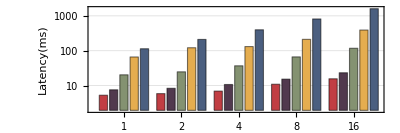

```mathematica
BarChart[
Transpose[{
Lookup[voltaGpuDurations,batches],
Lookup[p100GPUDurations,batches],
Lookup[k80GPUDurations,batches],
Lookup[p8CpuDurations,batches],
Lookup[E52686CpuDurations,batches]
}],
PlotTheme->"Detailed",
ScalingFunctions->"Log",
ChartStyle->{RGBColor["#C13E43"],RGBColor["#51394E"],RGBColor["#849271"],RGBColor["#E5AD4F"],RGBColor["#4B5F80"]},
AspectRatio->1/3,
ImageSize->Scaled[0.7],
FrameLabel->{"BatchSize","Latency(ms)"},
ChartLabels->{batches,None},
ChartLegends->{None,{"V100","P100","K80","P8","Xeon E52686"}}
]
```